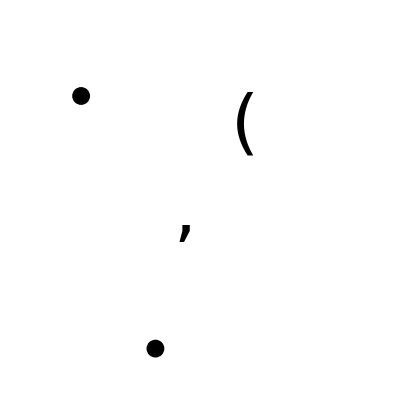

```mathematica
(*Random distribution of symbols*)
Graphics[{
Disk[{.5,8},.3],Disk[{3,-.5},.3],
Text[Style[",",100],{4,4}],
Text[Style["(",100],{6,7}],
Opacity[0],Line[{{-1,-1},{10,-1},{10,10}}],
}]
```

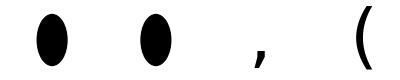

```mathematica
(*Sequence of symbols*)
Graphics[{
Disk[{0,0},.3],Disk[{2,0},.3],
Text[Style[",",100],{4,0}],
Rotate[Text[Style["(",100],{6,0}],Pi/8]
}]
```

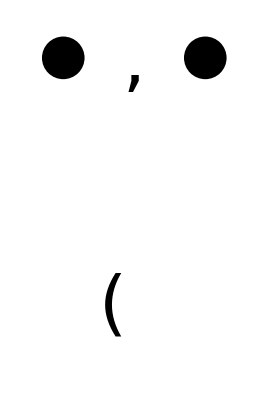

```mathematica
(*Happy face*)
Graphics[{
Disk[{0,0},.3],Disk[{2,0},.3],
Text[Style[",",500],{1,-.1}],
Rotate[Text[Style["(",300,Black],{.7,-3.5}],Pi/2],Opacity[0],Line[{{-.3,-2.5},{2.3,-2.5},{2.3,.3}}]
},PlotRange->{{-.55,2.5},{-4.3,.3}}]
```

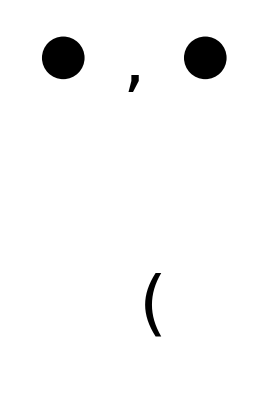

```mathematica
(*Sad face*)
Graphics[{
Disk[{0,0},.3],Disk[{2,0},.3],
Text[Style[",",500],{1,-.1}],
Rotate[Text[Style["(",300,Black],{1.26,-3.5}],-Pi/2],Opacity[0],Line[{{-.3,-2.5},{2.3,-2.5},{2.3,.3}}]
},PlotRange->{{-.55,2.5},{-4.3,.3}}]
```

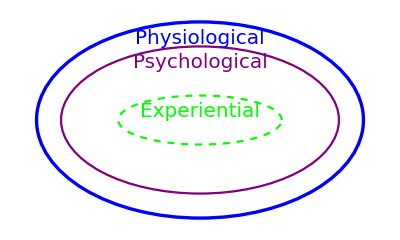

```mathematica
(*Constraints*)
Graphics[{Blue,Thickness[.006],
Circle[{0,0},{2,1.2}],
Text[Style["Physiological",20],{0,1}],
Purple,Thickness[.004],
Circle[{0,0},{1.7,.9}],
Text[Style["Psychological",20],{0,.7}],
Green,Dashed,
Circle[{0,0},{1.,.3}],
Text[Style["Experiential",20],{0,.1}]
}]
```

0.2

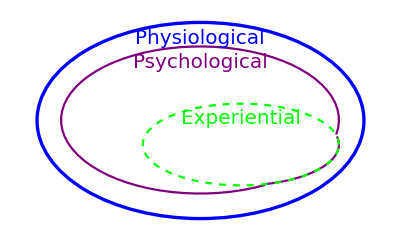

```mathematica
x=.2
Graphics[{Blue,Thickness[.006],
Circle[{0,0},{2,1.2}],
Text[Style["Physiological",20],{0,1}],
Purple,Thickness[.004],
Circle[{0,0},{1.7,.9},If[x>.069,{2Pi-10^x+.5,-Pi/9+3x/4},{0,2Pi}]],
If[x>.069,Circle[{.5,-.3},{1.+x,.3+x},{2Pi-10^(1.3x)+.5,2Pi}]],
If[x>.069,Circle[{.5,-.3},{1.+x,.3+x},{0,x}]],
Text[Style["Psychological",20],{0,.7}],
Green,Dashed,
Circle[{.5,-.3},{1.+x,.3+x}],
Text[Style["Experiential",20],{.5,.02}]
}]
```

```mathematica
horizon=Table[Graphics[{Blue,Thickness[.006],
Circle[{0,0},{2,1.2}],
Text[Style["Physiological",20],{0,1}],
Purple,Thickness[.004],
Circle[{0,0},{1.7,.9},If[x>.069,{2Pi-10^x+.5,-Pi/9+3x/4},{0,2Pi}]],
If[x>.069,Circle[{.5,-.3},{1.+x,.3+x},{2Pi-10^(1.3x)+.5,2Pi}]],
If[x>.069,Circle[{.5,-.3},{1.+x,.3+x},{0,x}]],
Text[Style["Psychological",20],{0,.7}],
Green,Dashed,
Circle[{.5,-.3},{1.+x,.3+x}],
Text[Style["Experiential",20],{0,.1}]
}],{x,0,.26,.002}];
```

```mathematica
Export["C:\\Users\\t_ziemer\\Desktop\\sonification-music\\sonification-and-music\\horizon3.mp4", horizon,"FrameRate"-> 15,"ControlAppearance"-> None]
```

C:\Users\t_ziemer\Desktop\sonification-music\sonification-and-music\horizon3.mp4

```mathematica
(*Animation for audio*)
tl=12;
anim=Table[Graphics[{Line[{{-8,-4.5},{8,-4.5},{8,4.5},{-8,4.5},{-8,-4.5}}],Text[Style["Working Memory",tl,Purple],{5.5*Sin[x],3*Cos[x+6Cos[x-4]]}],
Text[Style["Experience",tl,Green],{6*Cos[x+6Cos[x]],3*Sin[3+x+4*Sin[2x-.6]]}],
Text[Style["Interest",tl,Green],{6*Cos[x+6Cos[x]+2],3*Sin[3+x+4*Sin[2x-.6]]}],
Text[Style["Education",tl,Green],{6*Sin[x+6Cos[x]],3*Sin[3+x+4*Sin[2x]]}],
Text[Style["Absolute Thresholds",tl,Blue],{4*Cos[x],3*Sin[x+.3]}],
Text[Style["Masking Thresholds",tl,Blue],{4*Cos[x^2-5],3*Sin[x+Cos[x]+2.4]}],
Text[Style["Just Noticeable Differences",tl,Blue],{4*Sin[x],3*Cos[x+.3]}],
Text[Style["Schema Based Auditory Scene Analysis",tl,Purple],{3*Sin[x+Sin[x+Pi]],3*Cos[x+Pi/2]}],
Text[Style["Primitive Auditory Scene Analysis",tl,Purple],{3*Sin[x+Pi],3*Cos[x+Pi]}]
}],{x,0,32Pi,Pi/100}];
```

```mathematica
Export["C:\\Users\\t_ziemer\\Desktop\\sonification-music\\sonification-and-music\\anim.mp4",anim,"FrameRate"-> 25]
```